```mathematica
(*导入数据*)
Clear[data,i,L,n,temp];
L=100;n=25;data=Table[0,{i,L}];
For[i=1,i≤L,i++,
temp=StringJoin["E:\\study_materials\\MachineLearning\\HW2\\data\\data_",ToString[i]];
data[[i]]=Import[temp,"Table"];
];
```

```mathematica
(*2.lambda=10^(-10)*)
```

```mathematica
phi[i_,x_]:=N[E^(-(x-0.2 (i-12.5))^2),20]
```

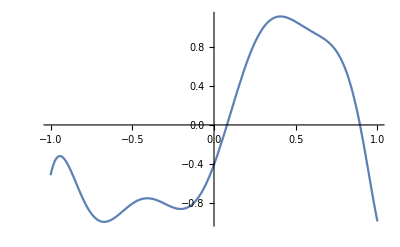
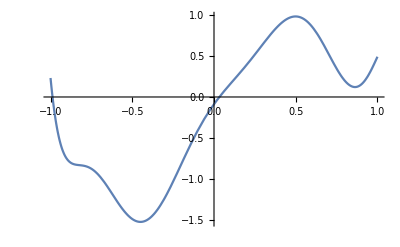
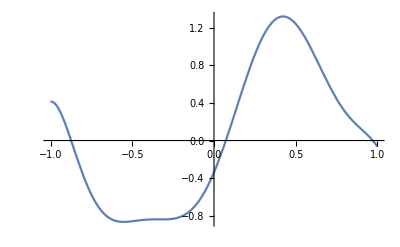
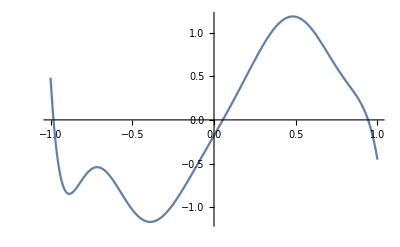
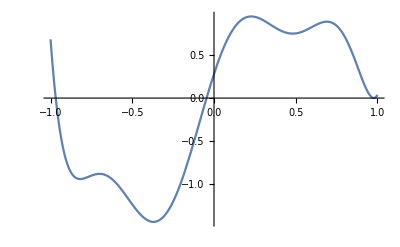
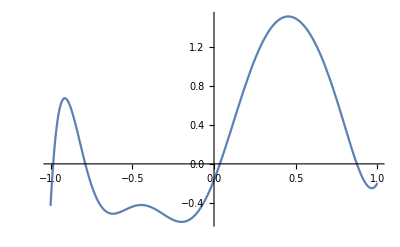
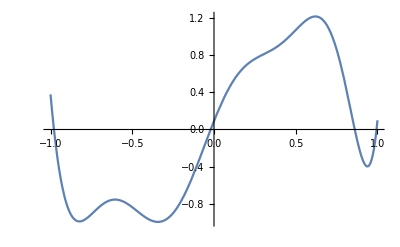
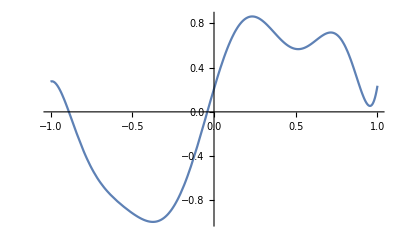

```mathematica
lambda=10^(-10);
img=Table[0,{i,L}];
For[l=1,l≤L,l++,
tempx=data[[l,All,1]];
tempy=data[[l,All,2]];
tempPhi=Table[phi[i,tempx],{i,24}];
tempPhi=Transpose[PrependTo[tempPhi,Table[1,{i,25}]]];
tempw=Inverse[(lambda*IdentityMatrix[25]+Transpose[tempPhi].tempPhi)].Transpose[tempPhi].tempy;
img[[l]]=Plot[Sum[tempw[[i+1]]*phi[i,x],{i,24}]+tempw[[1]],{x,-1,1}]
];
Table[img[[i]],{i,25}]
```

```mathematica
(*2.lambda=10^(-5)*)
```

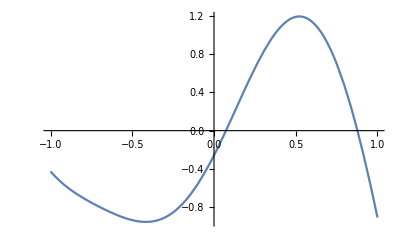
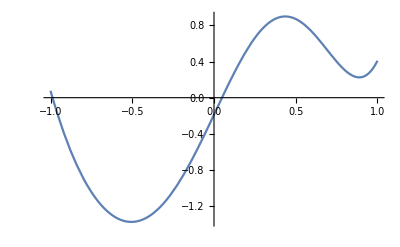
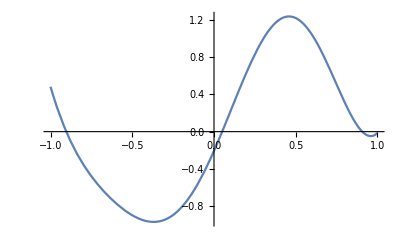
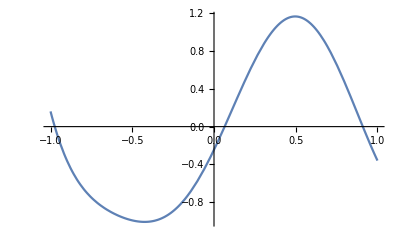
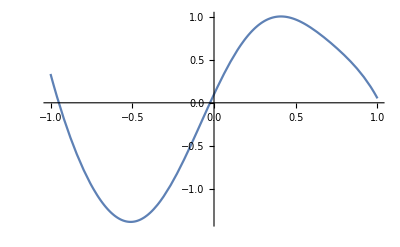
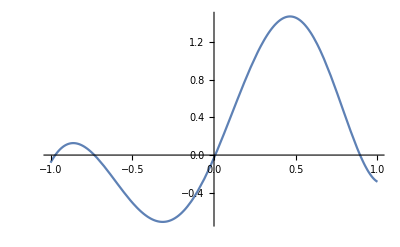
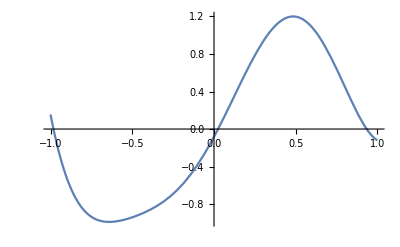
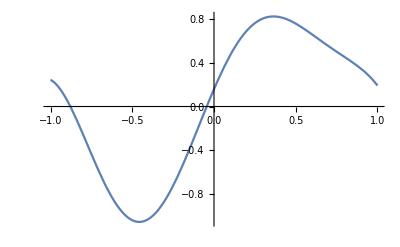

```mathematica
lambda=10^(-5);
img=Table[0,{i,L}];
For[l=1,l≤L,l++,
tempx=data[[l,All,1]];
tempy=data[[l,All,2]];
tempPhi=Table[phi[i,tempx],{i,24}];
tempPhi=Transpose[PrependTo[tempPhi,Table[1,{i,25}]]];
tempw=Inverse[(lambda*IdentityMatrix[25]+Transpose[tempPhi].tempPhi)].Transpose[tempPhi].tempy;
img[[l]]=Plot[Sum[tempw[[i+1]]*phi[i,x],{i,24}]+tempw[[1]],{x,-1,1}]
];
Table[img[[i]],{i,25}]
```

```mathematica
(*2.lambda=10^(-1)*)
```

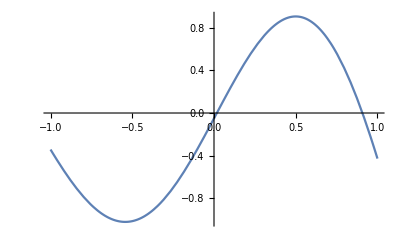
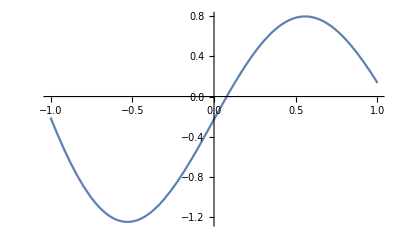
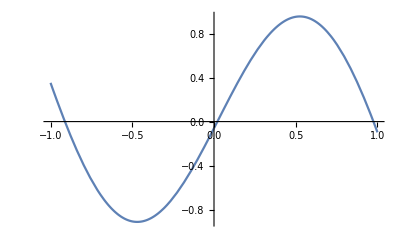
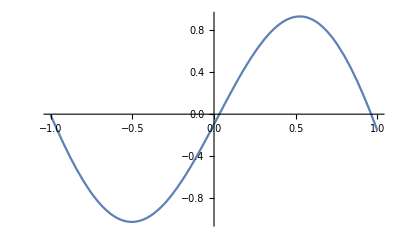
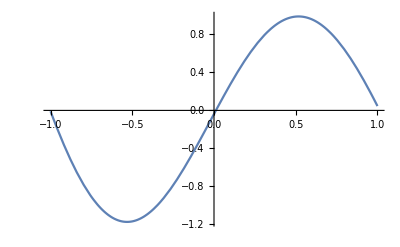
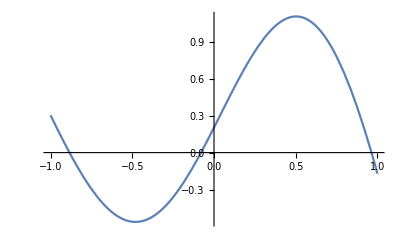
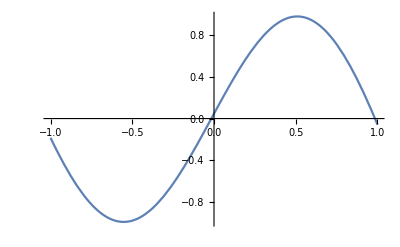
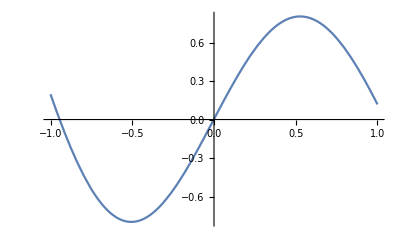

```mathematica
lambda=10^(-1);
img=Table[0,{i,L}];
For[l=1,l≤L,l++,
tempx=data[[l,All,1]];
tempy=data[[l,All,2]];
tempPhi=Table[phi[i,tempx],{i,24}];
tempPhi=Transpose[PrependTo[tempPhi,Table[1,{i,25}]]];
tempw=Inverse[(lambda*IdentityMatrix[25]+Transpose[tempPhi].tempPhi)].Transpose[tempPhi].tempy;
img[[l]]=Plot[Sum[tempw[[i+1]]*phi[i,x],{i,24}]+tempw[[1]],{x,-1,1}]
];
Table[img[[i]],{i,25}]
```

```mathematica
(*2.lambda=10^(1)*)
```

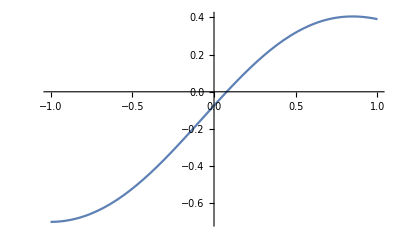
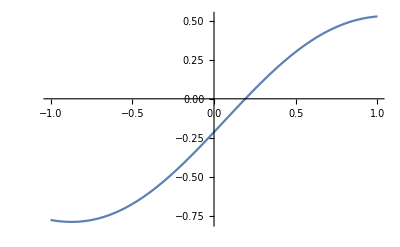
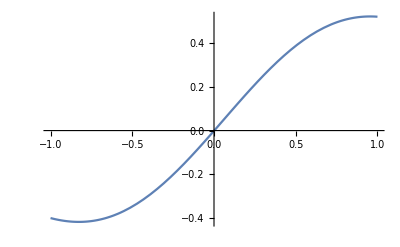
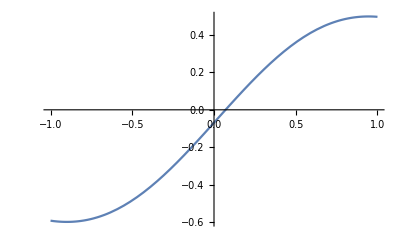
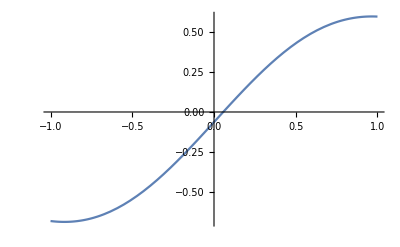
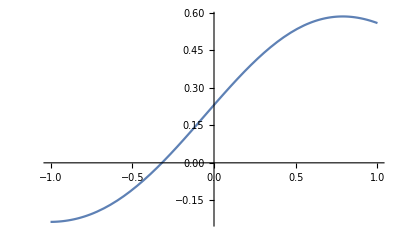
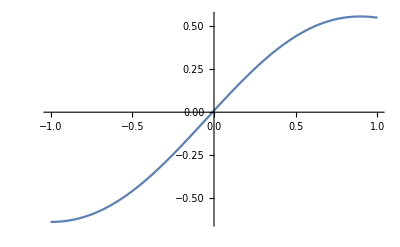
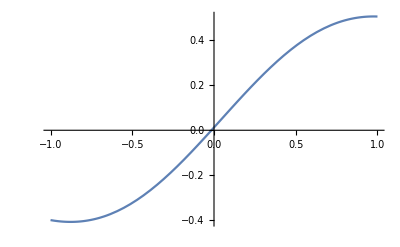

```mathematica
lambda=10^(1);
img=Table[0,{i,L}];
For[l=1,l≤L,l++,
tempx=data[[l,All,1]];
tempy=data[[l,All,2]];
tempPhi=Table[phi[i,tempx],{i,24}];
tempPhi=Transpose[PrependTo[tempPhi,Table[1,{i,25}]]];
tempw=Inverse[(lambda*IdentityMatrix[25]+Transpose[tempPhi].tempPhi)].Transpose[tempPhi].tempy;
img[[l]]=Plot[Sum[tempw[[i+1]]*phi[i,x],{i,24}]+tempw[[1]],{x,-1,1}]
];
Table[img[[i]],{i,25}]
```

```mathematica
(*3.*)
Clear[h,lambda,tempx,tempy,tempPhi,tempw,img,l,i];
h[x_]:=Sin[Pi x];
xn=data[[1,All,1]];
```

```mathematica
m=400;
deltax=N[4/m];
lam=Table[-3+i deltax,{i,0,m}];
list=Table[{lam[[i]],0,0,0},{i,m+1}];
For[k=1,k≤m+1,k++,
yx=0;
lambda=10^(lam[[k]]);
tempyx=0;
For[l=1,l≤L,l++,
tempx=data[[l,All,1]];
tempy=data[[l,All,2]];
tempPhi=Table[phi[i,tempx],{i,24}];
tempPhi=Transpose[PrependTo[tempPhi,Table[1,{i,25}]]];
tempw=Inverse[(lambda*IdentityMatrix[25]+Transpose[tempPhi].tempPhi)].Transpose[tempPhi].tempy;
tempyx+=(Sum[tempw[[i+1]]*phi[i,x],{i,24}]+tempw[[1]]);
];
(*生成平均估计*)
tempyx=tempyx/L;
(*生成bias^2*)
biasdiff=(tempyx/.x->xn)-h[xn];
list[[k,2]]=Sum[(biasdiff[[i]])^2,{i,1,n}]/n;
(*生成variance*)
list[[k,3]]=Sum[(data[[l,i,2]]-tempyx/.x->xn[[i]])^2,{l,100},{i,25}]/n/L;
(*生成bias^2+variance*)
list[[k,4]]=list[[k,2]]+list[[k,3]];
]
```

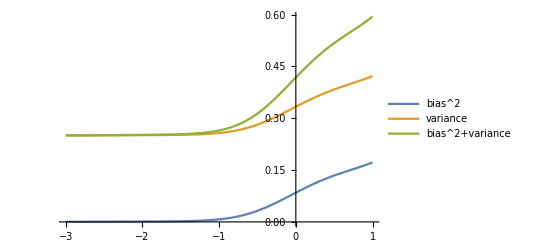

```mathematica
(*绘图*)
ListLinePlot[{list[[All,{1,2}]],list[[All,{1,3}]],list[[All,{1,4}]]},PlotLegends->{"bias^2","variance","bias^2+variance"}]
```